# Decision boundary Theory

```mathematica
fnew[dist_,fbase_, steps_, L_, r_, delta_] = (dist * L - dist  - r * Sum[((delta/(1+r))^t)*(fbase * L - fbase * t),{t, 1,steps}])/(L - 1 - r * Sum[((delta/(1+r))^t)*(L - t),{t, 1,steps}])
```

(-dist+dist L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

```mathematica
(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)
```

(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

30

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.25,1.23881,1.22875,1.21984,1.21204,1.20527,1.19945,1.1945,1.19032,1.18681,1.18389,1.18147,1.17947,1.17784,1.17651,1.17544,1.17457,1.17388,1.17333,1.1729,1.17256,1.1723,1.1721,1.17195,1.17184,1.17176,1.1717,1.17167,1.17165,1.17164,1.17164},{1.5,1.47761,1.45751,1.43969,1.42407,1.41053,1.3989,1.389,1.38064,1.37362,1.36777,1.36293,1.35895,1.35568,1.35302,1.35087,1.34914,1.34776,1.34666,1.34579,1.34511,1.34459,1.34419,1.34389,1.34367,1.34351,1.34341,1.34334,1.3433,1.34328,1.34328},{1.75,1.71642,1.68626,1.65953,1.63611,1.6158,1.59835,1.5835,1.57095,1.56043,1.55166,1.5444,1.53842,1.53352,1.52954,1.52631,1.52371,1.52164,1.51999,1.51869,1.51767,1.51689,1.51629,1.51584,1.51551,1.51527,1.51511,1.515,1.51494,1.51492,1.51492},{2.,1.95522,1.91502,1.87938,1.84814,1.82106,1.7978,1.778,1.76127,1.74724,1.73555,1.72586,1.71789,1.71136,1.70605,1.70175,1.69828,1.69551,1.69331,1.69158,1.69023,1.68918,1.68838,1.68778,1.68734,1.68703,1.68681,1.68667,1.68659,1.68656,1.68656}}

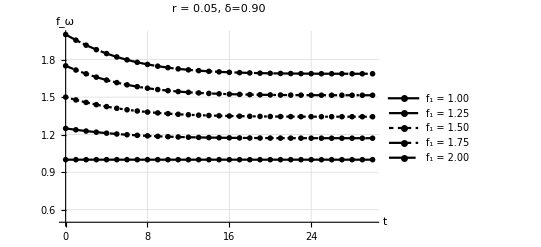

```mathematica
layers = 30
data = Table[Table[(factor -1 ) + fnew[1, factor,x,layers,0.05,0.9], {x,0,layers,1}], {factor, 1., 2., 0.25}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {0.5, 2.0}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.05, δ=0.90", PlotLegends->{"f_1 = 1.00", "f_1 = 1.25", "f_1 = 1.50", "f_1 = 1.75", "f_1 = 2.00"}, GridLines->Automatic, DataRange->{0, layers}]
```

```mathematica
XCLAIM
```

```mathematica
buffer = (1 + 0.1706) * (1 + 0.7634) 
f1 = 1 * buffer
```

2.06424

2.06424

12

{2.06424,2.01658,1.97639,1.94334,1.91685,1.8962,1.88057,1.86916,1.86122,1.85606,1.85309,1.85182,1.85182}

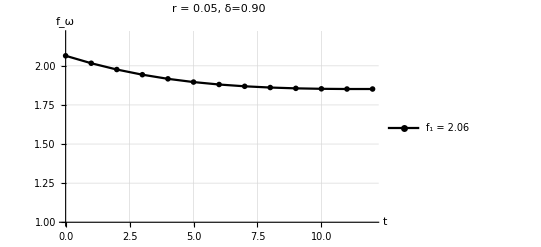

```mathematica
layers = 12
data = Table[(f1-1)+ fnew[1,f1,x,layers,0.05,0.9], {x,0,layers,1}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {1.0, 2.2}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.05, δ=0.90", PlotLegends->{"f_1 = 2.06"}, GridLines->Automatic, DataRange->{0, layers}]
```

```mathematica
fomega = Last[data]
```

1.85182

```mathematica
1.9797603487667936
```

```mathematica
1.9797603487667936
```

1.97976

```mathematica
1.8518166645938126
reduction = 1 - (fomega/f1)
```

1.85182

0.102905